```mathematica
R=7.5;
frac=.5;
pad=1.8;
damping=1.5;
radius=Floor[R]+Floor[pad];
size=2radius+1;
sigma=6.;
qmax=Ceiling[sigma R];
```

```mathematica
filter=RotateLeft[Table[Exp[-damping(i^2+j^2+k^2)/radius^2],{i,-radius,radius},{j,-radius,radius},{k,-radius,radius}],{radius,radius,radius}];

support=Map[#+(Floor[R]+Floor[pad]+1){1,1,1}&,Select[Flatten[Table[{i,j,k},{i,-Floor[R],Floor[R]},{j,-Floor[R],Floor[R]},{k,-Floor[R],Floor[R]}],2],Norm[#]<R&]];

mask=ReplacePart[Table[0,{size},{size},{size}],support->1.];
```

```mathematica
density=Nest[smooth[binaryContrast[#]]&,RandomReal[{0,1},{size,size,size}],4];
```

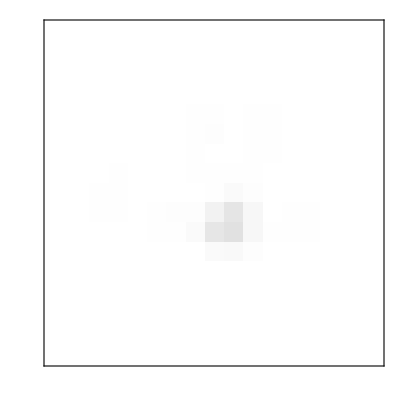
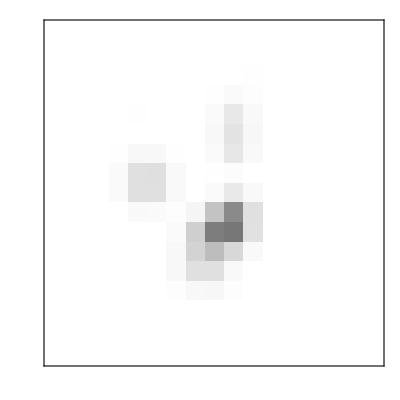
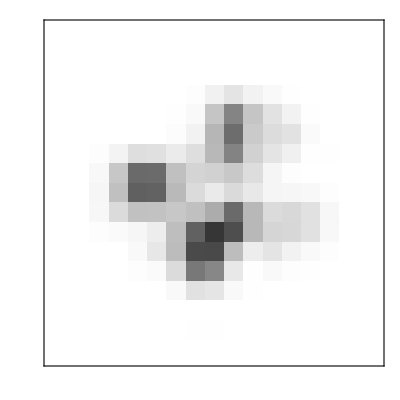
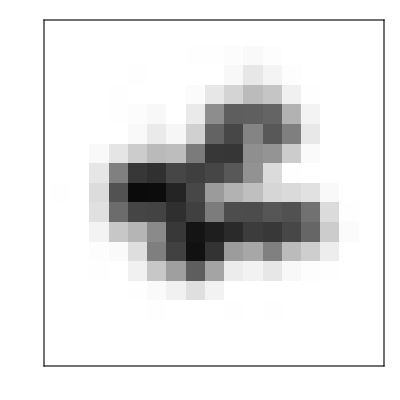
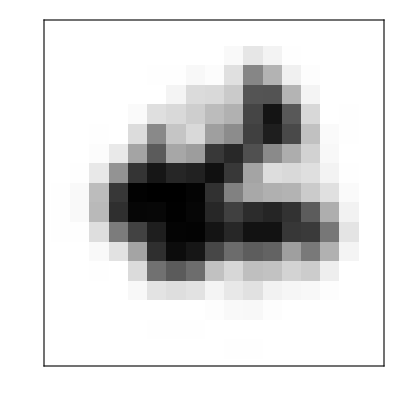
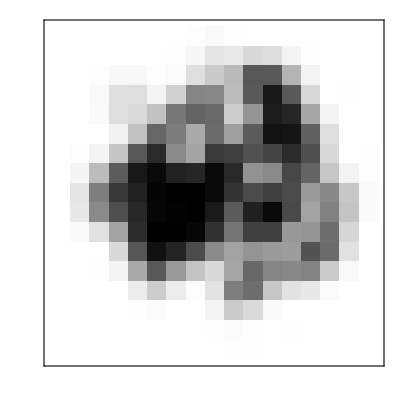
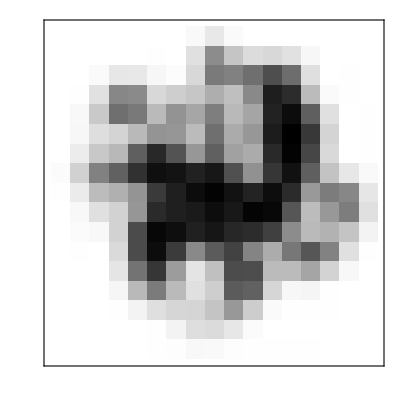
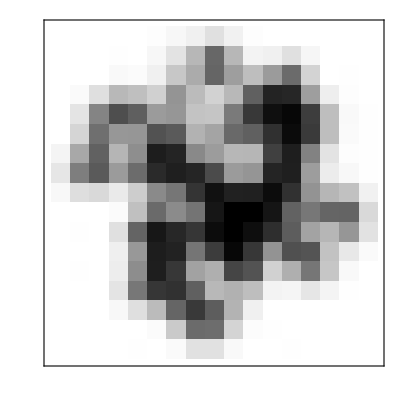

```mathematica
renderStack[density]
```

```mathematica
render3D[density]
```

-Graphics3D-

```mathematica
padding=Select[Flatten[Table[{i,j,k},{i,-Floor[pad],Floor[pad]},{j,-Floor[pad],Floor[pad]},{k,-Floor[pad],Floor[pad]}],2],Norm[#]<pad&];

paddedSupport=Union[Flatten[Outer[Plus,support,padding,1],1]];
```

```mathematica
Export[NotebookDirectory[]<>"density.dat",Flatten[density,1]];
```

```mathematica
Export[NotebookDirectory[]<>"support.dat",Prepend[Map[#-{1,1,1}&,paddedSupport],{qmax,Length[paddedSupport]}]];
```